Quantum Computation and Visualization of Hamiltonians Using Discrete Quantum Mechanics and IBM QISKit

Raffaele Miceli and Michael McGuigan, arXiv:1812.01044v1 [quant-ph] (2018)
Notebook: Óscar Amaro, December 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

Main takeaway:
- analytical equalities may be exact in theory, but in matrix form may lead to inconsistencies that then reflect on different eigenspectra.

## Figure 1

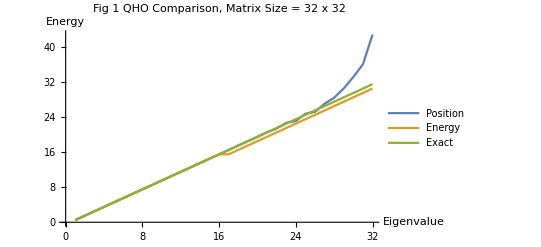

```mathematica
(* n=5 can be very slow on some computers *)
Clear[n,A,Adg,Id,Idtil,HhoEnergy,HhoPos,HhoEnergyE,X,P,Xpos,Ppos,F,Fdg]

(* number of qubits*)
n=5;

Id=ParallelTable[i-j ,{i,1,2^n,1},{j,1,2^n,1}];

(* equation 5: define A *)
A=ParallelTable[Sqrt[j]i-1-j ,{i,1,2^n,1},{j,1,2^n,1}];

(* define A dagger *)
Adg=ConjugateTranspose[A];

(* equation 17 *)
Adg.A-A.Adg;

(* using this form would give the exact result for the eigenenergies*)
A.Adg+Id/2 ;

(* equation 14: we use this instead  *) 
HhoEnergy=0.5(A.Adg+Adg.A);
(* eigenvalues will appear in reverse order*)
HhoEnergyE=Eigenvalues[HhoEnergy];

ordE=Ordering[HhoEnergyE];
HhoEnergyE=HhoEnergyE[[ordE]];

(* equation 6: position momentum operators  *)
(*X=1/(√2)(Adg+A);P=I/(√2)(Adg-A);*)
Xpos=Sqrt[(2π)/2^n]Table[(2j-1-2^n)/2 i-j ,{i,1,2^n,1},{j,1,2^n,1}];

F=1/Sqrt[2^n] Table[Exp[(2π I)/2^n((2i-1-2^n)/2)((2j-1-2^n)/2)] ,{i,1,2^n,1},{j,1,2^n,1}];
Fdg=ConjugateTranspose[F]//N;
Ppos=F.Xpos.Fdg//N;

(* equation 18: (P.P+X.X)/2 would give the exact result, instead we use  *)
Idtil=Adg.A-A.Adg;
HhoPos = ((Xpos.Xpos//N)+(Ppos.Ppos//N))/2//Chop;
HhoPosE=Eigenvalues[HhoPos];
ordP=Ordering[HhoPosE];
HhoPosE=HhoPosE[[ordP]];

(* equation 13: exact theoretical values *)
HhoExactE=ParallelTable[i+0.5,{i,0,2^n-1,1}];

(* compare *)
ListPlot[{HhoPosE,HhoEnergyE,HhoExactE},PlotLegends->{"Position","Energy","Exact"},Joined->True,AxesLabel->{"Eigenvalue","Energy"},PlotLabel->"Fig 1 QHO Comparison, Matrix Size = 32 x 32"]
```

## Figures 3 and 4

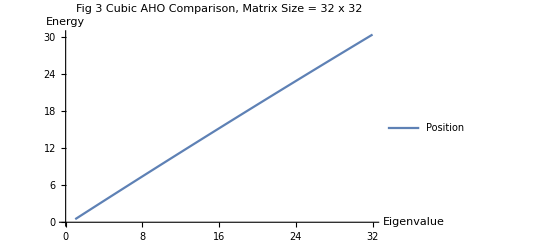

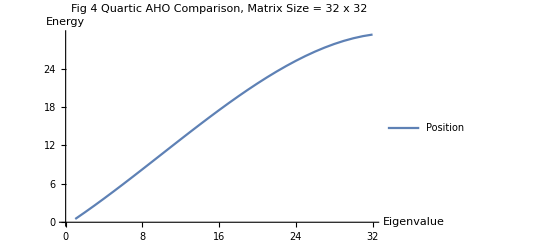

```mathematica
(*  *)
Clear[n,A,Adg,Id,Idtil,HhoEnergy,HhoPos,HhoEnergyE,X,P,Xpos,Ppos,F,Fdg,λ]

n=5;
λ=0.05;
HcubExactE=ParallelTable[(i+0.5)-(5λ^2)/12(i^2+i+11/30),{i,0,2^n-1,1}];
HquaExactE=ParallelTable[(i+0.5)+(3λ)/8(i^2+i+1/2)-λ^2/64(17i^3+51/2 i^2+59/2 i+21/2),{i,0,2^n-1,1}];


ListPlot[{HcubExactE},PlotLegends->{"Position","Energy","Exact"},Joined->True,AxesLabel->{"Eigenvalue","Energy"},PlotLabel->"Fig 3 Cubic AHO Comparison, Matrix Size = 32 x 32"]

(* equation 22 does not seem to reproduce figure 4*)
ListPlot[{HquaExactE},PlotLegends->{"Position","Energy","Exact"},Joined->True,AxesLabel->{"Eigenvalue","Energy"},PlotLabel->"Fig 4 Quartic AHO Comparison, Matrix Size = 32 x 32"]
```